## 情報数学レポート 1SC16309Y田中雅也

## 課題

### 問題1.

次の関数の極値を求めよ.
f(x,y) =sinx+siny-sin(x+y)

#### 関数のグラフの概形を描いてみる.

```mathematica
F = Sin[x]+Sin[y]-Sin[x+y];
Plot3D[F,{x,0,2π},{y,0,2π}]
```

-Graphics3D-

#### xでの偏微分とyでの偏微分が0になる点 (x,y) を求める.

```mathematica
D[F,x]
```

Cos[x]-Cos[x+y]

```mathematica
D[F,y]
```

Cos[y]-Cos[x+y]

```mathematica
Solve[{D[F,x]==0,D[F,y]==0},{x,y}]
```

{{x→ConditionalExpression[2 π C[1],C[1]∈ℤ],y→ConditionalExpression[2 π C[2],C[2]∈ℤ]},{x→ConditionalExpression[-(2 π)/3+2 π C[1],C[1]∈ℤ],y→ConditionalExpression[-(2 π)/3+2 π C[2],C[2]∈ℤ]},{x→ConditionalExpression[(2 π)/3+2 π C[1],C[1]∈ℤ],y→ConditionalExpression[(2 π)/3+2 π C[2],C[2]∈ℤ]}}

(x, y) を実数とすると, 解は (0, 0) と ((2π)/3, (2π)/3) と((4π)/3,(4π)/3)である.

#### 判別式 H (x, y) を計算する.

```mathematica
D[D[F,x],y] (* Subscript[f, xy] *)
```

Sin[x+y]

```mathematica
D[F,{x,2}] (* Subscript[f, xx] *)
```

-Sin[x]+Sin[x+y]

```mathematica
D[F,{y,2}] (* Subscript[f, yy] *)
```

-Sin[y]+Sin[x+y]

```mathematica
H=D[F,{x,2}] D[F,{y,2}]-(D[D[F,x],y])^2
```

-Sin[x+y]^2+(-Sin[x]+Sin[x+y]) (-Sin[y]+Sin[x+y])

#### H (0, 0) を計算する.

```mathematica
H/.{x->0,y->0}
```

0

Hが0なので (0, 0) は極値ではない.

#### H ((2π)/3, (2π)/3) を計算する.

```mathematica
H/.{x->(2π)/3 ,y->(2π)/3}
```

9/4

Hが正なので ((2π)/3, (2π)/3) は極値である.

#### H ((4π)/3, (4π)/3) を計算する.

```mathematica
H/.{x->(4π)/3 ,y->(4π)/3}
```

9/4

Hが正なので ((4π)/3, (4π)/3) は極値である.

#### f_xx((2π)/3,(2π)/3)を計算する.

```mathematica
D[F,{x,2}]
```

-Sin[x]+Sin[x+y]

```mathematica
D[F,{x,2}]/.{x->(2π)/3,y->(3π)/3}
```

-√3

f_xx が負なので極値は極大値である.

#### f_xx((4π)/3,(4π)/3)を計算する.

```mathematica
D[F,{x,2}]
```

-Sin[x]+Sin[x+y]

```mathematica
D[F,{x,2}]/.{x->(4π)/3,y->(4π)/3}
```

√3

f_xx が正なので極値は極小値である.

#### まとめ

f(x,y) = sinx+siny-sin(x+y) は ((2π)/3,(2π)/3)に極大値(3 √3)/2,((4π)/3,(4π)/3)に極小値(-3 √3)/2 を持つ.

### 問題2.

定積分 ∫_0^(π/2) Sin[θ]/(1+Sin[θ])ⅆθ を求めよ.

#### 関数のグラフの概形を描いてみる.

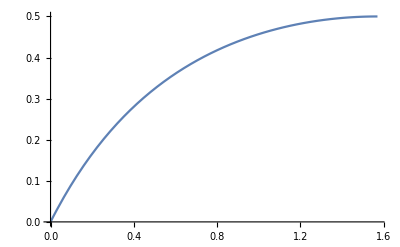

```mathematica
F=Sin[θ]/(1+Sin[θ]);
Plot[F,{θ,0,π/2}]
```

#### 極値を求めてみる.

```mathematica
D[F,θ]
```

-(Cos[θ] Sin[θ])/(1+Sin[θ])^2+Cos[θ]/(1+Sin[θ])

```mathematica
Solve[D[F,θ]==0,θ]
```

{{θ→ConditionalExpression[π/2+2 π C[1],C[1]∈ℤ]}}

```mathematica
F/.θ-> π/2
```

1/2

```mathematica
N[π/2]
```

1.5708

sinθ/(1+sinθ)は, [0,π/2]区間では θ=π/2 のとき極大値 1/2 をとる.

#### 定積分を計算する.

```mathematica
Integrate[Sin[θ]/(1+Sin[θ]),{θ,0,π/2}]
```

1/2 (-2+π)

∫_0^(π/2) sinθ/(1+sinθ)ⅆθ =1/2(-2+π)

### 問題3.

次の関数の極値を求めよ.
f(x,y)=x y (x^2+y^2-1)

#### 関数のグラフの概形を描いてみる.

```mathematica
F =x y (x^2+y^2-1);
Plot3D[F,{x,-2,2},{y,-2,2}]
```

-Graphics3D-

#### xでの偏微分とyでの偏微分が0になる点 (x,y) を求める.

```mathematica
D[F,x]
```

2 x^2 y+y (-1+x^2+y^2)

```mathematica
D[F,y]
```

2 x y^2+x (-1+x^2+y^2)

```mathematica
Solve[{D[F,x]==0,D[F,y]==0},{x,y}]
```

{{x→-1/2,y→-1/2},{x→-1/2,y→1/2},{x→0,y→-1},{x→0,y→1},{x→1/2,y→-1/2},{x→1/2,y→1/2},{x→-1,y→0},{x→0,y→0},{x→1,y→0}}

(x, y) を実数とすると, 解は (0,±1 ) と (±1/2, ±1/2) (復号任意)と(±1,0)と(0,0)である.

#### 判別式 H (x, y) を計算する.

```mathematica
D[D[F,x],y] (* Subscript[f, xy] *)
```

-1+3 x^2+3 y^2

```mathematica
D[F,{x,2}] (* Subscript[f, xx] *)
```

6 x y

```mathematica
D[F,{y,2}] (* Subscript[f, yy] *)
```

6 x y

```mathematica
H=D[F,{x,2}] D[F,{y,2}]-(D[D[F,x],y])^2
```

36 x^2 y^2-(-1+3 x^2+3 y^2)^2

#### H (0, 0) を計算する.

```mathematica
H/.{x->0,y->0}
```

-1

Hが負なので (0, 0) は極値ではない.

#### H (1/2, 1/2) を計算する.

```mathematica
H/.{x->1/2 ,y->1/2}
```

2

Hが正なので (1/2, 1/2) は極値である.

#### H (1/2, -1/2) を計算する.

```mathematica
H/.{x->1/2 ,y->-1/2}
```

2

Hが正なので (1/2, -1/2) は極値である.

#### H (-1/2, 1/2) を計算する.

```mathematica
H/.{x->-1/2 ,y->1/2}
```

2

Hが正なので (-1/2, 1/2) は極値である.

#### H (-1/2, -1/2) を計算する.

```mathematica
H/.{x->-1/2 ,y->-1/2}
```

2

Hが正なので (-1/2, -1/2) は極値である.

#### H (0,1) を計算する.

```mathematica
H/.{x->0,y->1}
```

-4

Hが負なので (0, 1) は極値ではない.

#### H (0,-1) を計算する.

```mathematica
H/.{x->0,y->-1}
```

-4

Hが負なので (0, -1) は極値ではない.

#### H (1,0) を計算する.

```mathematica
H/.{x->1,y->0}
```

-4

Hが負なので (1,0 ) は極値ではない.

#### H (-1,0) を計算する.

```mathematica
H/.{x->-1,y->0}
```

-4

Hが負なので (-1, 0) は極値ではない.

#### f_xx(1/2,1/2)を計算する.

```mathematica
D[F,{x,2}]
```

6 x y

```mathematica
D[F,{x,2}]/.{x->1/2,y->1/2}
```

3/2

f_xx が正なので極値は極小値である.

#### f_xx(1/2,-1/2)を計算する.

```mathematica
D[F,{x,2}]
```

6 x y

```mathematica
D[F,{x,2}]/.{x->1/2,y->-1/2}
```

-3/2

f_xx が負なので極値は極大値である.

#### f_xx(-1/2,1/2)を計算する.

```mathematica
D[F,{x,2}]
```

6 x y

```mathematica
D[F,{x,2}]/.{x->-1/2,y->1/2}
```

-3/2

f_xx が負なので極値は極大値である.

#### f_xx(-1/2,-1/2)を計算する.

```mathematica
D[F,{x,2}]
```

6 x y

```mathematica
D[F,{x,2}]/.{x->-1/2,y->-1/2}
```

3/2

f_xx が正なので極値は極小値である.

#### まとめ

f(x,y)=x y (x^2+y^2-1) は (±1/2,±1/2)（複合逆順）に極大値 1/8 に(±1/2,±1/2)（複合同順）に極小値-1/8 を持つ.

### 問題4.

定積分 ∫_0^1 log (1+√x)ⅆx  を求めよ.

#### 関数のグラフの概形を描いてみる.

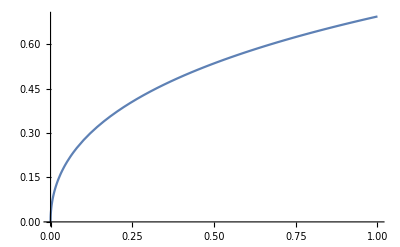

```mathematica
F=Log[1+√x];
Plot[F,{x,0,1}]
```

#### 極値を求めてみる.

```mathematica
D[F,x]
```

1/(2 (1+√x) √x)

```mathematica
Solve[D[F,x]==0,x]
```

{{x→ComplexInfinity}}

log(1+√x)は, [0,1]区間では極値を持たない.

#### 定積分を計算する.

```mathematica
Integrate[Log[1+√x],{x,0,1}]
```

1/2

∫_0^(π/2) sinθ/(1+sinθ)ⅆθ =1/2

### 問題5.

次の関数の極値を求めよ.
f(x,y)=x^4+y^4-2 x^2+4 x y - 2 y^2

#### 関数のグラフの概形を描いてみる.

```mathematica
F = x^4+y^4-2 x^2+4 x y - 2 y^2;
Plot3D[F,{x,-1,1},{y,-1,1}]
```

-Graphics3D-

#### xでの偏微分とyでの偏微分が0になる点 (x,y) を求める.

```mathematica
D[F,x]
```

-4 x+4 x^3+4 y

```mathematica
D[F,y]
```

4 x-4 y+4 y^3

```mathematica
Solve[{D[F,x]==0,D[F,y]==0},{x,y}]
```

{{x→0,y→0},{x→-(-1)^(1/6),y→ⅈ-(-1)^(1/6)},{x→(-1)^(1/6),y→-ⅈ+(-1)^(1/6)},{x→-(-1)^(5/6),y→ⅈ-(-1)^(5/6)},{x→(-1)^(5/6),y→-ⅈ+(-1)^(5/6)},{x→-√2,y→√2},{x→√2,y→-√2}}

(x, y) を実数とすると, 解は (±√2,± √2) と (±(-1)^(1/6),±(ⅈ-(-1)^(1/6)))と(±(-1)^(5/6),±(ⅈ-(-1)^(5/6)))（複合逆順）
である.

#### 判別式 H (x, y) を計算する.

```mathematica
D[D[F,x],y] (* Subscript[f, xy] *)
```

4

```mathematica
D[F,{x,2}] (* Subscript[f, xx] *)
```

-4+12 x^2

```mathematica
D[F,{y,2}] (* Subscript[f, yy] *)
```

-4+12 y^2

```mathematica
H=D[F,{x,2}] D[F,{y,2}]-(D[D[F,x],y])^2
```

-16+(-4+12 x^2) (-4+12 y^2)

#### H (√2, -√2) を計算する.

```mathematica
H/.{x->√2,y->-√2}
```

384

Hが正なので (-√2, √2) は極値ではない.

#### H (-√2, √2) を計算する.

```mathematica
H/.{x->-√2,y->√2}
```

384

Hが正なので (-√2, √2) は極値ではない.

#### f_xx(√2,-√2)を計算する.

```mathematica
D[F,{x,2}]
```

-4+12 x^2

```mathematica
D[F,{x,2}]/.{x->√2,y->-√2}
```

20

f_xx が正なので極値は極小値である.

#### f_xx(-√2,√2)を計算する.

```mathematica
D[F,{x,2}]
```

-4+12 x^2

```mathematica
D[F,{x,2}]/.{x->-√2,y->√2}
```

20

f_xx が正なので極値は極小値である.

#### まとめ

f(x,y)=x^4+y^4-2 x^2+4 x y - 2 y^2 は (±√2,±√2)（複合逆順）に極小値-8を持つ.